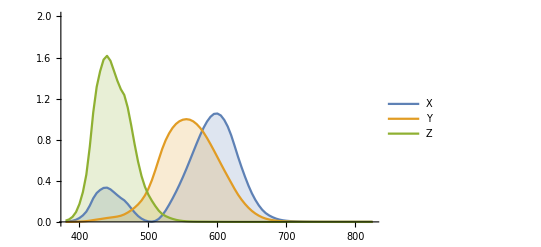

{380.,385.,390.,395.,400.,405.,410.,415.,420.,425.,430.,435.,440.,445.,450.,455.,460.,465.,470.,475.,480.,485.,490.,495.,500.,505.,510.,515.,520.,525.,530.,535.,540.,545.,550.,555.,560.,565.,570.,575.,580.,585.,590.,595.,600.,605.,610.,615.,620.,625.,630.,635.,640.,645.,650.,655.,660.,665.,670.,675.,680.,685.,690.,695.,700.,705.,710.,715.,720.,725.,730.,735.,740.,745.,750.,755.,760.,765.,770.,775.,780.,785.,790.,795.,800.,805.,810.,815.,820.,825.}

```mathematica
{λ,x,y,z}=Import["/mnt/BC4A45D34A458B5A/Dev/mathematica_notebooks/Others/ciexyzjv.csv"]ᵀ;
xyzCieTabPlot=ListLinePlot[{{λ,x}ᵀ,{λ,y}ᵀ,{λ,z}ᵀ},PlotLegends->{"X","Y","Z"},PlotRange->{0,2},Filling->Axis]
λ//N
```

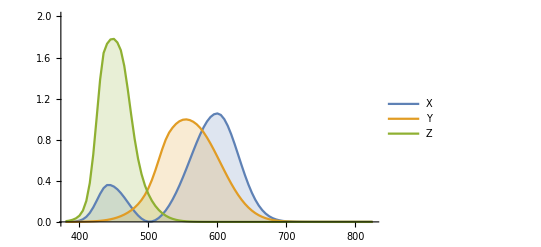

```mathematica
xFit1931[wave_Real]:=Block[{t1,t2,t3},
t1=(wave-442.0)*If[wave<442.0,0.0624,0.0374];
t2=(wave-599.8)*If[wave<599.8,0.0264,0.0323];
t3=(wave-501.1)*If[wave<501.1,0.0490,0.0382];
0.362Exp[-0.5*t1*t1]+1.056Exp[-0.5*t2*t2]-0.065*Exp[-0.5*t3*t3]
];
yFit1931[wave_Real]:=Block[{t1,t2},
t1=(wave-568.8)*If[wave<568.8,0.0213,0.0247];
t2=(wave-530.9)*If[wave<530.9,0.0613,0.0322];
0.821Exp[-0.5*t1*t1]+0.286Exp[-0.5*t2*t2]
];
zFit1931[wave_Real]:=Block[{t1,t2},
t1=(wave-437.0)*If[wave<437.0,0.0845,0.0278];
t2=(wave-459.0)*If[wave<459.0,0.0385,0.0725];
1.217Exp[-0.5*t1*t1]+0.681Exp[-0.5*t2*t2]
];

SetAttributes[{xFit1931,yFit1931,zFit1931},Listable];
xx=Map[xFit1931,λ];
yy=Map[yFit1931,λ];
zz=Map[zFit1931,λ];
ListLinePlot[{{λ,xx}ᵀ,{λ,yy}ᵀ,{λ,zz}ᵀ},PlotLegends->{"X","Y","Z"},PlotRange->{0,2},Filling->Axis]
```

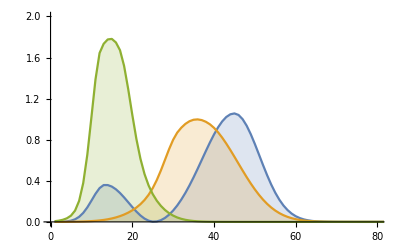

```mathematica
ListLinePlot[Through[{xFit1931,yFit1931,zFit1931}[λ]],Filling->Axis,PlotRange->{{0,80},{0,2}}]
```

```mathematica
(*Piecewise fit*)
SetAttributes[{cieX,cieY,cieZ},Listable];
cieX[λ_]:={0.362,1.056,-0.065}.Exp[-MapThread[(λ-#1) Piecewise[{{#2,λ<#1},{#3,True}}]&,{{442.0,599.8,501.1},{0.0624,0.0264,0.0490},{0.0374,0.0323,0.0382}}]^2/2]

cieY[λ_]:={0.821,0.286}.Exp[-MapThread[(λ-#1) Piecewise[{{#2,λ<#1},{#3,True}}]&,{{568.8,530.9},{0.0213,0.0613},{0.0247,0.0322}}]^2/2]

cieZ[λ_]:={1.217,0.681}.Exp[-MapThread[(λ-#1) Piecewise[{{#2,λ<#1},{#3,True}}]&,{{437.0,459.0},{0.0845,0.0385},{0.0278,0.0725}}]^2/2]
```

```mathematica
xxx=Map[cieX,λ]; yyy=Map[cieY,λ]; zzz=Map[cieZ,λ];
```

```mathematica
xSE=Power[(x-xxx),2]; ySE=Power[(y-yyy),2]; zSE=Power[(z-zzz),2];
xMSE=Mean[xSE] 
yMSE=Mean[ySE] 
zMSE=Mean[zSE]
Mean[{xMSE,yMSE,zMSE}]//ScientificForm
```

0.000448017

0.0000284617

0.01191

4.12883×10^-3

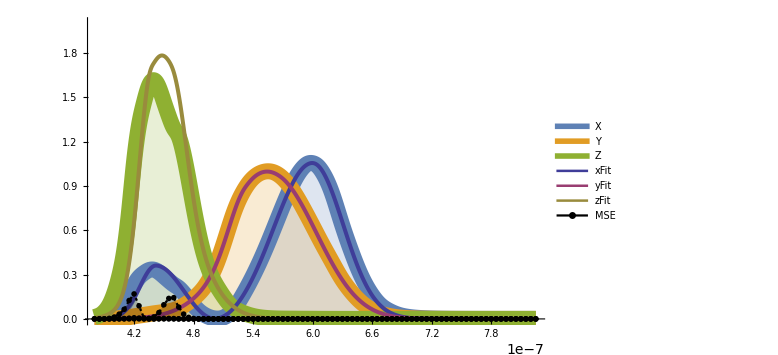

```mathematica
Show[
ListLinePlot[{{λ,x}ᵀ,{λ,y}ᵀ,{λ,z}ᵀ},PlotLegends->{"X","Y","Z"},PlotRange->{0,2},Filling->Axis,PlotStyle->Directive[Thickness[0.02]],InterpolationOrder->3],
ListLinePlot[{{λ,xxx}ᵀ,{λ,yyy}ᵀ,{λ,zzz}ᵀ},PlotRange->{0,2},PlotStyle->Directive[Thickness[0.005]],PlotTheme->"Classic",InterpolationOrder->3,PlotLegends->{"xFit","yFit","zFit"}],
ListLinePlot[{{λ,xSE}ᵀ,{λ,ySE}ᵀ,{λ,zSE}ᵀ},PlotRange->{0,2},Filling->Axis,PlotTheme->"Monochrome",PlotLegends->{"MSE"}]
,ImageSize->Large]
```

```mathematica
sRGBGamma=Function[x,With[{z=Abs[x]},Sign[x] Piecewise[{{12.92 z,z≤0.0031308}},1.055 z^(1/2.4)-0.055]],Listable];

myVisibleSpectrum[λ_]:=RGBColor@@Clip[sRGBGamma[{{3.2404542,-1.5371385,-0.49853141},{-0.96926603,1.8760108,0.041556017},{0.055643431,-0.20402591,1.0572252}}.Through[{cieX,cieY,cieZ}[λ]]],{0,1}]
```

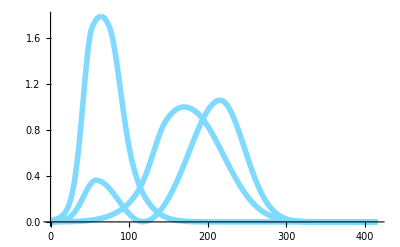

```mathematica
cieXYZ=Through[XYZColor[cieX,cieY,cieZ][#]]&;

{d1,d2}=Transpose/@Table[List@@fn[λ],{fn,{cieXYZ,newVisibleSpectrum}},{λ,385,800}];

Show[ListLinePlot[d1,PlotStyle->Directive[Thickness[0.01],Hue[0.55,0.5,1]],PlotTheme->"Pastel",InterpolationOrder->3],ListLinePlot[d2,PlotStyle->Directive[Black,Dashed]]]
```

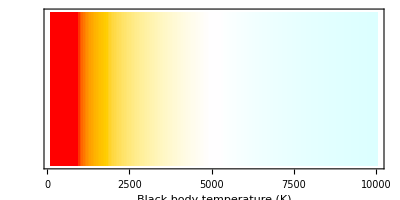

```mathematica
λ=λ 10^-9;(*wavelength is given in nm*)

XYZ[t_]:=Module[{h=6.62607*10^-34,c=2.998*10^8,k=1.38065*10^-23},{x,y,z}.((2 h c^2)/((-1+E^((h c/k)/(t λ))) λ^5))//#/#[[2]]&]

Graphics[Table[{ColorConvert[XYZColor@@XYZ[i],"RGB"],Rectangle[{i,0},{i+50,5000}]},{i,100,10000,50}],Frame->True,FrameTicks->{Automatic,None,None,None},FrameLabel->{"Black body temperature (K)","","",""}]
```